```mathematica
(*Mathematica*)
```

```mathematica
A[n_]:=Table[If[m==k,0,If[m<k,(-1)^(m+k),-(-1)^(m+k)]],{k,1,n},{m,1,n}]
```

```mathematica
A[4]+IdentityMatrix[4]
```

{{1,1,-1,1},{-1,1,1,-1},{1,-1,1,1},{-1,1,-1,1}}

```mathematica
(*S0(4) group Sum*)
```

```mathematica
SO4={{1,1,-1,1},{-1,1,1,-1},{1,-1,1,1},{-1,1,-1,1}}
```

{{1,1,-1,1},{-1,1,1,-1},{1,-1,1,1},{-1,1,-1,1}}

```mathematica
Det[SO4]
```

8

```mathematica
Tr[SO4]
```

4

```mathematica
u[1]=N[Eigenvalues[SO4]]
```

{1.+2.41421 ⅈ,1.-2.41421 ⅈ,1.+0.414214 ⅈ,1.-0.414214 ⅈ}

```mathematica
p[x_]=CharacteristicPolynomial[SO4,x]
```

8-16 x+12 x^2-4 x^3+x^4

```mathematica
o[z_,1]=Integrate[p[x]^2,{x,-z,z}]
```

128 z+(896 z^3)/3+(576 z^5)/5+(80 z^7)/7+(2 z^9)/9

```mathematica
w[3]=z/.NSolve[o[z,1]-1==0,z]
```

{-0.0050613-0.729456 ⅈ,-0.0050613+0.729456 ⅈ,-0.000190553-2.94759 ⅈ,-0.000190553+2.94759 ⅈ,1.37957×10^-6-6.24616 ⅈ,1.37957×10^-6+6.24616 ⅈ,0.00134478-1.78712 ⅈ,0.00134478+1.78712 ⅈ,0.00781139}

```mathematica
r=N[(1+I)/Sqrt[2]]
```

0.707107+0.707107 ⅈ

```mathematica
Abs[r]
```

1.

```mathematica
rc=-Conjugate[r]
```

-0.707107+0.707107 ⅈ

```mathematica
SO4c={{1,r,-r,r},
{-rc,1,r,-r},
{rc,-rc,1,r},
{-rc,rc,-rc,1}}
```

{{1,0.707107+0.707107 ⅈ,-0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ},{0.707107-0.707107 ⅈ,1,0.707107+0.707107 ⅈ,-0.707107-0.707107 ⅈ},{-0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,1,0.707107+0.707107 ⅈ},{0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,1}}

```mathematica
Det[SO4c]//Chop
```

-11.6569

```mathematica
Tr[SO4c]
```

4

```mathematica
u[2]=N[Eigenvalues[SO4c]]
```

{2.76537,1.84776,-1.84776,1.23463}

```mathematica
q[x_]=CharacteristicPolynomial[SO4c,x]//Chop
```

-11.6569+13.6569 x-4. x^3+x^4

```mathematica
o[z_,2]=Integrate[q[x]^2,{x,-z,z}]
```

0.+271.765 z+124.34 z^3-53.0274 z^5+4.57143 z^7+0.222222 z^9

```mathematica
w[4]=z/.NSolve[o[z,2]-1==0,z]
```

{-2.30494-0.520539 ⅈ,-2.30494+0.520539 ⅈ,-0.00129329-1.15706 ⅈ,-0.00129329+1.15706 ⅈ,2.31333×10^-6-5.41426 ⅈ,2.31333×10^-6+5.41426 ⅈ,0.00367963,2.3044-0.520079 ⅈ,2.3044+0.520079 ⅈ}

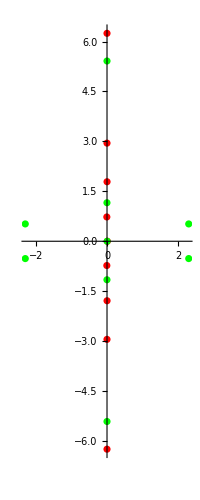

```mathematica
ComplexListPlot[{w[3],w[4]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
w[1]=x/.NSolve[p[x]==0,x]
```

{1.-2.41421 ⅈ,1.+2.41421 ⅈ,1.-0.414214 ⅈ,1.+0.414214 ⅈ}

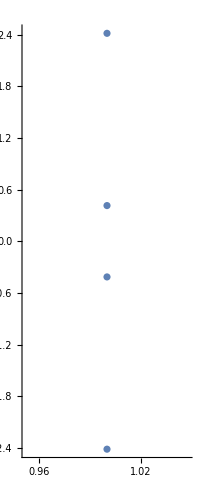

```mathematica
ComplexListPlot[w[1]]
```

```mathematica
w[2]=x/.NSolve[q[x]==0,x]
```

{-1.84776,1.23463,1.84776,2.76537}

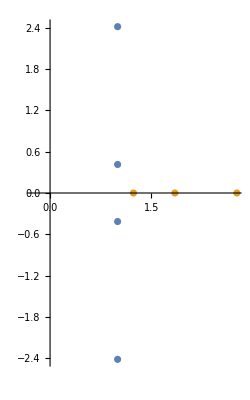

```mathematica
ComplexListPlot[{w[1],w[2]},PlotRange->All]
```

```mathematica
SO44c=SO4.SO4c
```

{{3.12132-2.12132 ⅈ,0.292893+2.12132 ⅈ,-0.292893-0.707107 ⅈ,0.292893-0.707107 ⅈ},{-1.70711+0.707107 ⅈ,1.70711-2.12132 ⅈ,1.70711+2.12132 ⅈ,-1.70711-0.707107 ⅈ},{0.292893+0.707107 ⅈ,-0.292893+0.707107 ⅈ,0.292893-2.12132 ⅈ,3.12132+2.12132 ⅈ},{1.12132-2.12132 ⅈ,-1.12132+0.707107 ⅈ,1.12132+0.707107 ⅈ,-1.12132-2.12132 ⅈ}}

```mathematica
Det[SO44c]//Chop
```

-93.2548

```mathematica
Tr[SO44c]
```

4.-8.48528 ⅈ

```mathematica
u[3]=N[Eigenvalues[SO44c]]
```

{3.97995-4.95443 ⅈ,-3.30334-3.43407 ⅈ,1.99713-0.697209 ⅈ,1.32626+0.600432 ⅈ}

```mathematica
s[x_]=CharacteristicPolynomial[SO44c,x]//Chop
```

-93.2548+(95.598+13.6569 ⅈ) x-(25.6569+24.9706 ⅈ) x^2-(4.-8.48528 ⅈ) x^3+x^4

```mathematica
o[z_,3]=Integrate[s[x]^2,{x,-z,z}]
```

(0.+0. ⅈ)+17392.9 z+(9158.48+4845.59 ⅈ) z^3-(459.325-1117.77 ⅈ) z^5-(30.6611+33.6638 ⅈ) z^7+0.222222 z^9

```mathematica
o[z_,4]=Integrate[p[x]*q[z],{x,-z,z}]
```

-186.51 z+218.51 z^2-93.2548 z^3+45.2548 z^4+11.3373 z^5-26.5373 z^6+8 z^7-1.6 z^8+(2 z^9)/5

```mathematica
w[5]=z/.NSolve[o[z,4]==0,z]
```

{-1.84776,0.,0.-1.50134 ⅈ,0.+1.50134 ⅈ,0.-4.2126 ⅈ,0.+4.2126 ⅈ,1.23463,1.84776,2.76537}

```mathematica
w[6]=z/.NSolve[o[z,3]-1==0,z]
```

{-12.2937-5.05773 ⅈ,-4.53063-1.85808 ⅈ,-1.91162-2.5632 ⅈ,-0.185849-1.33117 ⅈ,0.0000574946-5.29488×10^-14 ⅈ,0.185791+1.33116 ⅈ,1.91162+2.56321 ⅈ,4.53063+1.85808 ⅈ,12.2937+5.05773 ⅈ}

```mathematica
(*root test as ones and zero*)
```

```mathematica
FullSimplify[Table[o[w[3][[j]],1],{j,Length[w[3]]}]]//Chop
```

{1.,1.,1.,1.,1.-5.82077×10^-10 ⅈ,1.+5.82077×10^-10 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[4][[j]],2],{j,Length[w[4]]}]]//Chop
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[5][[j]],4],{j,Length[w[4]]}]]//Chop
```

{0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[Table[o[w[6][[j]],3],{j,Length[w[6]]}]]//Chop
```

{1.-7.56234×10^-7 ⅈ,1.-6.98492×10^-10 ⅈ,1.,1.,1.,1.,1.,1.+6.98492×10^-10 ⅈ,0.999999-5.73695×10^-7 ⅈ}

```mathematica
ph[x_,1]=x^2*q[x]/p[x]
```

(x^2 (-11.6569+13.6569 x-4. x^3+x^4))/(8-16 x+12 x^2-4 x^3+x^4)

```mathematica
ph[z_,2]=z^2*(o[z,2]-1)/(o[z,1]-1)
```

(z^2 (-1.+271.765 z+124.34 z^3-53.0274 z^5+4.57143 z^7+0.222222 z^9))/(-1+128 z+(896 z^3)/3+(576 z^5)/5+(80 z^7)/7+(2 z^9)/9)

```mathematica
g1=JuliaSetPlot[ph[x,1]/N[2],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x,1]/N[2],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_SO4_Group_Sum_Hermanrings_scale2_both.jpg",{g1,g2}]
```

Julia_SO4_Group_Sum_Hermanrings_scale2_both.jpg

```mathematica
(*end*)
```